```mathematica
ClearAll["Global`*"]
```

### erif_TESTS

#### erf

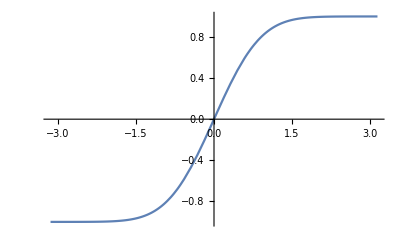
{-Graphics-,-Graphics-}

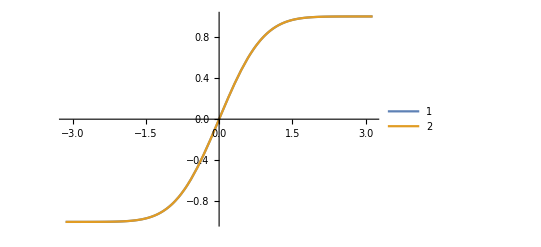

```mathematica
erf2[x_]:=2/Sqrt[π]*Integrate[Exp[-t^2],{t,0,x}];
p1=Plot[Erf[x],{x,-π,π},PlotLegends->Automatic];
p2=Plot[erf2[x],{x,-π,π},PlotLegends->Automatic];
{p1,p2}
Plot[{Erf[x],erf2[x]},{x,-π,π},PlotLegends->Automatic]
```

#### erfi

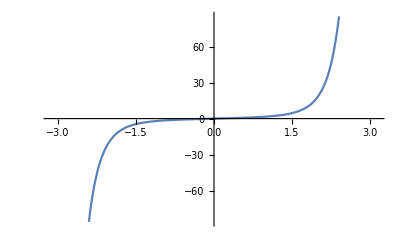
{-Graphics-,-Graphics-,-Graphics-}

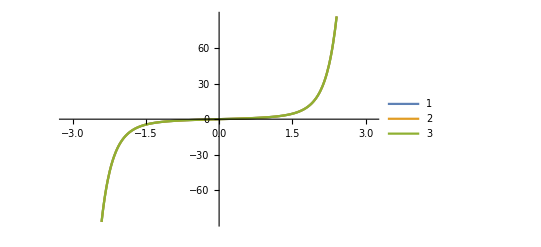

```mathematica
erfi2[x_]:=-I*2/Sqrt[π]*Integrate[Exp[-t^2],{t,0,I*x}];
erfi3[x_]:=-I*Erf[I*x];
p4=Plot[Erfi[x],{x,-π,π},PlotLegends->Automatic];
p5=Plot[erfi2[x],{x,-π,π},PlotLegends->Automatic];
p6=Plot[erfi3[x],{x,-π,π},PlotLegends->Automatic];
{p4,p5,p6}
Plot[{Erfi[x],erfi2[x],erfi3[x]},{x,-π,π},PlotLegends->Automatic]
```

#### erf, erfi

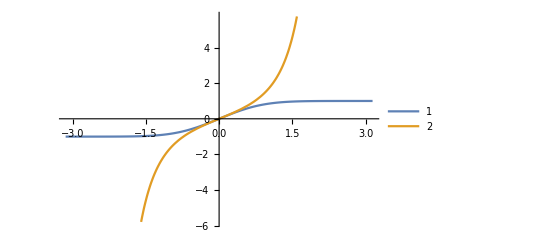
{-Graphics-,-Graphics-}

```mathematica
p7=Plot[{Erf[x],-I*Erf[I*x]},{x,-π,π},PlotLegends->Automatic];
p8=Plot[{Erf[x],Erfi[x]},{x,-π,π},PlotLegends->Automatic];
{p7,p8}
```

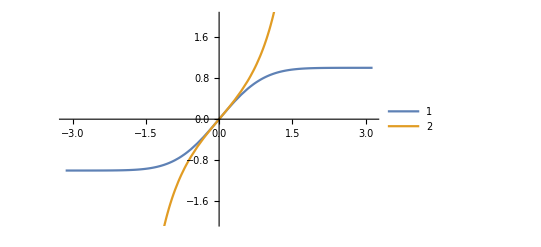

```mathematica
Show[p7,{PlotRange->{-2,2}}]
```

### Difference between Normal and VonMises distribution

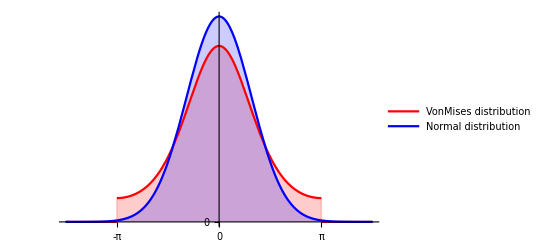

```mathematica
Plot[{PDF[VonMisesDistribution[0,1],x],PDF[NormalDistribution[0,1],x]},{x,-1.5Pi,1.5Pi},PlotRange->All,Filling->Axis,PlotStyle->{Red,Blue},PlotLegends->Placed[{"VonMises distribution","Normal distribution"},{0.8,0.8}],Ticks->{Table[i*π/2,{i,-4,4}]}]
```

### Hi-density function in the paper. *periodic > ρ in the paper -90 ~ +90 > ρ in Mathematica: -180 ~ +180

```mathematica
ρ[θ_,b_]:=4*Sqrt[b/(2 π)]*Exp[b*(Cos[2 θ]+1)]/Erfi[Sqrt[2 b]]
κ[b_]:=1/4*Integrate[ρ[θ,b]*Sin[θ]^3,{θ,0,π}]
```

```mathematica
N[κ[x]/.x->100]
κ[x]/.x->0.001
κ[0.001]//N
```

0.00250633

0.333244

-7.84875×10^-8

```mathematica
bb=Table[{i,κ[x]/.x->i},{i,0.001,20,0.5}];
```

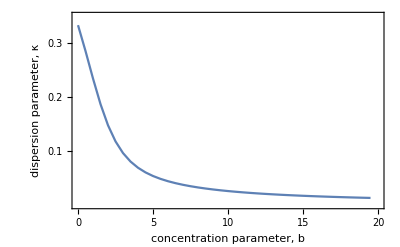

```mathematica
ListLinePlot[bb,
PlotRange->{{0,20},{0,0.35}},
Frame->True,
FrameTicks->{{{0.1,0.2,0.3},None},{{0,5,10,15,20},None}},
LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black},
FrameLabel->{"concentration parameter, b","dispersion parameter, κ"}
]
```

```mathematica
findroot[target_]:=FindRoot[κ[b]==target,{b,0.01}];
```

```mathematica
w1=findroot/@{0.33,0.3,0.2,0.1}
w0=findroot/@{0.33,0.15,0.1,0.05}
```

{{b→0.0372385},{b→0.353871},{b→1.35461},{b→2.89849}}

{{b→0.0372385},{b→1.96673},{b→2.89849},{b→5.32972}}

```mathematica
t0=findroot/@{1/3,4/15,1/5,2/15,1/15}
```

{{b→3.49038×10^-9},{b→0.683476},{b→1.35461},{b→2.22191},{b→4.12029}}

```mathematica
t0b=Table[t0[[i,1,2]],{i,1,5}]
w1b=Table[w1[[i,1,2]],{i,1,4}]
w0b=Table[w0[[i,1,2]],{i,1,4}]
```

{3.49038×10^-9,0.683476,1.35461,2.22191,4.12029}

{0.0372385,0.353871,1.35461,2.89849}

{0.0372385,1.96673,2.89849,5.32972}

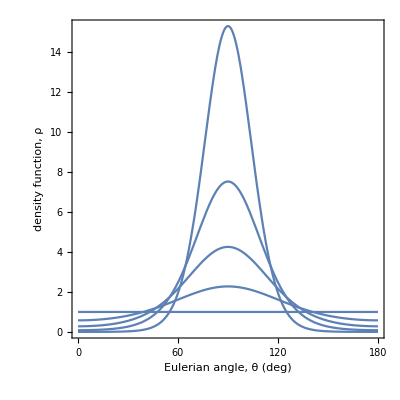

```mathematica
Plot[ρ[θ Degree -90 Degree,t0b],{θ,0,180},
PlotRange->{{0,180},All},
FrameTicks->{{Table[2i,{i,0,8}],None},{Table[30i,{i,0,6}],None}},
LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black},
Frame->True,
FrameLabel->{"Eulerian angle, θ (deg)","density function, ρ"},
AspectRatio->1/1
](*This is the same with the figure in the paper*)
```

```mathematica
Max[t0b]
```

4.12029

```mathematica
t0b
```

{3.49038×10^-9,0.683476,1.35461,2.22191,4.12029}

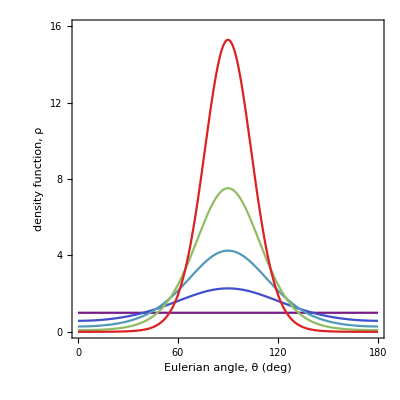

```mathematica
klist={1/3,4/15,1/5,2/15,1/15};
Show[
Table[
Plot[ρ[θ Degree -90 Degree,t],{θ,0,180},
PlotRange->{{0,180},All},
PlotStyle->ColorData["Rainbow"][t/Max[t0b]],
FrameTicks->{{Table[2i,{i,0,15}],None},{Table[30i,{i,0,6}],None}},
LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black},
Frame->True,
FrameLabel->{"Eulerian angle, θ (deg)","density function, ρ"},
AspectRatio->1/1
],
{t,t0b}
],
PlotRange->{{0,180},{0,16}}]
```

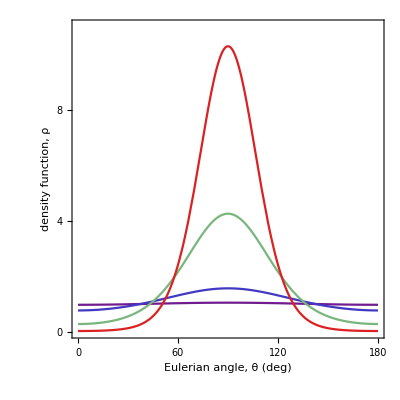

```mathematica
klist={0.33,0.3,0.2,0.1};
Show[
Table[
Plot[ρ[θ Degree -90 Degree,t],{θ,0,180},
PlotRange->{{0,180},All},
PlotStyle->ColorData["Rainbow"][t/Max[w1b]],
FrameTicks->{{Table[2i,{i,0,15}],None},{Table[30i,{i,0,6}],None}},
LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black},
Frame->True,
FrameLabel->{"Eulerian angle, θ (deg)","density function, ρ"},
AspectRatio->1/1
],
{t,w1b}
],
PlotRange->{{0,180},{0,11}}]
```

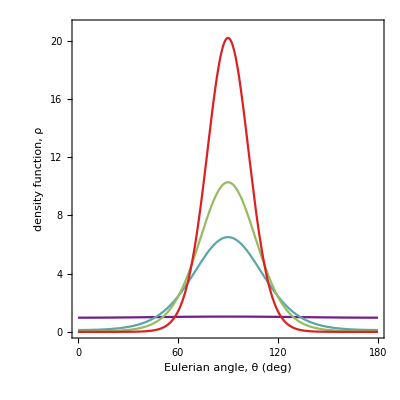

```mathematica
klist={0.33,0.15,0.1,0.05};
Show[
Table[
Plot[ρ[θ Degree -90 Degree,t],{θ,0,180},
PlotRange->{{0,180},All},
PlotStyle->ColorData["Rainbow"][t/Max[w0b]],
FrameTicks->{{Table[2i,{i,0,15}],None},{Table[30i,{i,0,6}],None}},
LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black},
Frame->True,
FrameLabel->{"Eulerian angle, θ (deg)","density function, ρ"},
AspectRatio->1/1
],
{t,w0b}
],
PlotRange->{{0,180},{0,21}}]
```

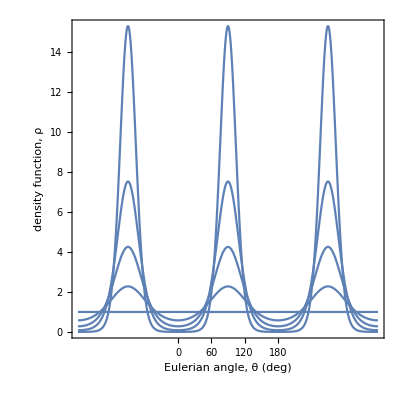

```mathematica
(*The VonMises density function is periodic*)
Plot[ρ[θ Degree -90 Degree,{t0b}],{θ,-180,360},
PlotRange->{{-180,360},All},
FrameTicks->{{Table[2i,{i,0,8}],None},{Table[30i,{i,0,6}],None}},
LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black},
Frame->True,
FrameLabel->{"Eulerian angle, θ (deg)","density function, ρ"},
AspectRatio->1/1
]
```

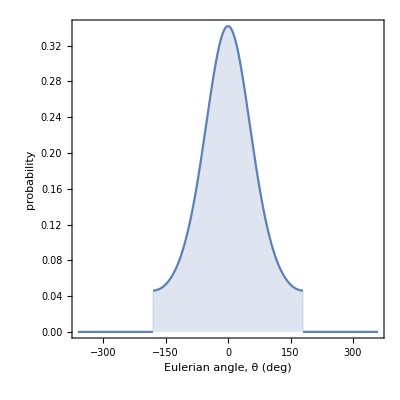

```mathematica
(*VonMises distribution in Mathematica cut at 180, -180 degree*)
Plot[PDF[VonMisesDistribution[0 Degree,1],x Degree],{x,-360 ,360 },
PlotRange->{{-360, 360 },Automatic},Filling->Axis,
Frame->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black},
FrameLabel->{"Eulerian angle, θ (deg)","probability"},
AspectRatio->1]
```

### Hii-PDF

#### In degree (do not sue)

```mathematica
pdf[θ_,b_]:=ρ[θ Degree,b]/Integrate[ρ[x Degree,b],{x,-90,90}]
area[b_]:=Integrate[ρ[x Degree,b],{x,-90,90}]//N
```

```mathematica
testA1=area[2]
```

368.563

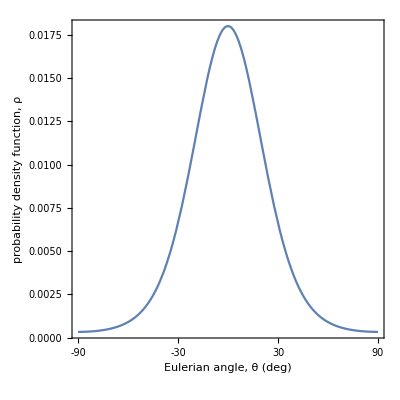

```mathematica
Plot[ρ[θ Degree,2]/testA1,{θ,-90,90},
PlotRange->{{-90,90},All},
FrameTicks->{{Automatic,None},{Table[30i,{i,-3,3}],None}},
LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black},
Frame->True,
FrameLabel->{"Eulerian angle, θ (deg)","probability density function, ρ"},
AspectRatio->1/1
]
```

#### In radian

```mathematica
rho[θ_,b_]:=4*Sqrt[b/(2 π)]*Exp[b*(Cos[2 θ]+1)]/Erfi[Sqrt[2 b]]
kappa[b_]:=1/4*Integrate[ρ[θ,b]*Sin[θ]^3,{θ,0,π}]
```

```mathematica
findroot[target_]:=FindRoot[kappa[b]==target,{b,0.01}];
```

```mathematica
kappalist={0.33,0.3,0.2,0.15,0.1,0.05}
wb=findroot/@kappalist;
wb=Table[wb[[i,1,2]],{i,1,6}]
```

{0.33,0.3,0.2,0.15,0.1,0.05}

{0.0372385,0.353871,1.35461,1.96673,2.89849,5.32972}

```mathematica
pdf[θ_,b_]:=rho[θ ,b]/NIntegrate[rho[x ,b],{x,-π/2,π/2}]
```

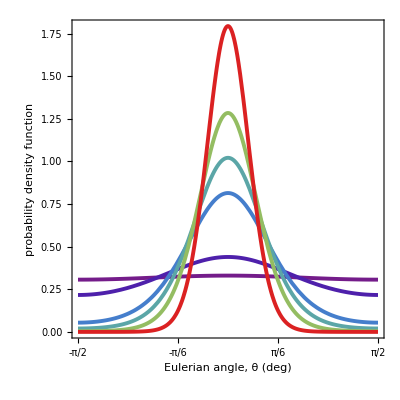

```mathematica
klist={0.33,0.3,0.2,0.15,0.1,0.05};
pdfAll=Show[
Table[
Plot[pdf[θ ,t],{θ,-π/2,π/2},
PlotRange->{{-π/2,π/2},All},
PlotStyle->{Thickness[0.007],ColorData["Rainbow"][t/Max[wb]]},
FrameTicks->{{Automatic,None},{Table[π/6i,{i,-3,3}],None}},
LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black},
Frame->True,
FrameLabel->{"Eulerian angle, θ (deg)","probability density function"},
AspectRatio->1/1
],
{t,wb}
],
PlotRange->{{-π/2,π/2},All}]
```

```mathematica
pdf1[θ_]:=pdf[θ,wb[[1]]](*kappa=0.33*)
pdf2[θ_]:=pdf[θ,wb[[2]]](*kappa=0.3*)
pdf3[θ_]:=pdf[θ,wb[[3]]](*kappa=0.2*)
pdf4[θ_]:=pdf[θ,wb[[4]]](*kappa=0.15*)
pdf5[θ_]:=pdf[θ,wb[[5]]](*kappa=0.1*)
pdf6[θ_]:=pdf[θ,wb[[6]]](*kappa=0.05*)
```

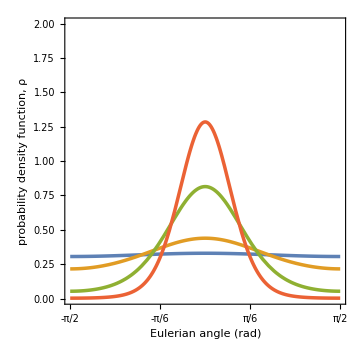
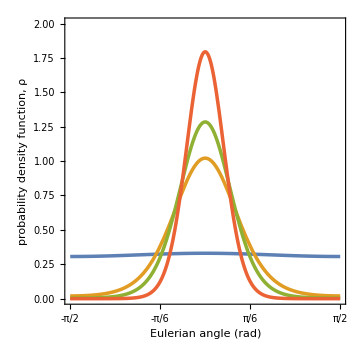

```mathematica
(*w1: kappa=(0.33, 0.3, 0.2, 0.1) -> 1,2,3,5*)
pw1=Plot[{pdf1[θ],pdf2[θ],pdf3[θ],pdf5[θ]},{θ,-π/2,π/2},
PlotRange->{{-π/2,π/2},{0,2}},
FrameTicks->{{Automatic,None},{Table[π/6i,{i,-3,3}],None}},
LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black},
Frame->True,
FrameLabel->{"Eulerian angle (rad)","probability density function, ρ"},
AspectRatio->1/1,
PlotStyle->{Thickness[0.007]},
ImageSize->Medium
];
(*w0: kappa=(0.33, 0.15, 0.1, 0.05) -> 1,4,5,6*)
pw0=Plot[{pdf1[θ],pdf4[θ],pdf5[θ],pdf6[θ]},{θ,-π/2,π/2},
PlotRange->{{-π/2,π/2},{0,2}},
FrameTicks->{{Automatic,None},{Table[π/6i,{i,-3,3}],None}},
LabelStyle->{FontSize->14,FontFamily->"Helvetica",Black},
Frame->True,
FrameLabel->{"Eulerian angle (rad)","probability density function, ρ"},
AspectRatio->1/1,
PlotStyle->{Thickness[0.007]},
ImageSize->Medium
];
{pw1,pw0}
```

```mathematica
NIntegrate[pdf1[x],{x,-π/2,π/2}];
NIntegrate[pdf2[x],{x,-π/2,π/2}];
NIntegrate[pdf3[x],{x,-π/2,π/2}];
NIntegrate[pdf4[x],{x,-π/2,π/2}];
NIntegrate[pdf5[x],{x,-π/2,π/2}];
NIntegrate[pdf6[x],{x,-π/2,π/2}];
```

```mathematica
D1=ProbabilityDistribution[pdf1[x],{x,-π/2,π/2}];(*kappa=0.33*)
D2=ProbabilityDistribution[pdf2[x],{x,-π/2,π/2}];(*kappa=0.3*)
D3=ProbabilityDistribution[pdf3[x],{x,-π/2,π/2}];(*kappa=0.2*)
D4=ProbabilityDistribution[pdf4[x],{x,-π/2,π/2}];(*kappa=0.15*)
D5=ProbabilityDistribution[pdf5[x],{x,-π/2,π/2}];(*kappa=0.1*)
D6=ProbabilityDistribution[pdf6[x],{x,-π/2,π/2}];(*kappa=0.05*)
```

```mathematica
(*w1: kappa=(0.33, 0.3, 0.2, 0.1) -> 1,2,3,5*)
(*w0: kappa=(0.33, 0.15, 0.1, 0.05) -> 1,4,5,6*)
n=100;
w1Fang=Round[RandomVariate[D1,n]*180/π+90,1];
w1FEang=Round[RandomVariate[D2,n]*180/π+90,1];
w1E1ang=Round[RandomVariate[D3,n]*180/π+90,1];
w1E2ang=Round[RandomVariate[D5,n]*180/π+90,1];

w0Fang=Round[RandomVariate[D1,n]*180/π+90,1];
w0FEang=Round[RandomVariate[D4,n]*180/π+90,1];
w0E1ang=Round[RandomVariate[D5,n]*180/π+90,1];
w0E2ang=Round[RandomVariate[D6,n]*180/π+90,1];
```

```mathematica
AngleLine[x_]:={{Re[Exp[I x Degree]],Im[Exp[I x Degree]]},{Re[Exp[I (x+180) Degree]],Im[Exp[I (x+180) Degree]]}};
(*x here should be in degree*)
fiberDist[list_]:=
Module[{x=list},
ListLinePlot[Table[AngleLine/@x],PlotRange->{{-1.05,1.05},{-1.05,1.05}},AspectRatio->1,ImageSize->Small,PlotStyle->Directive[{Darker[Green],Thickness[0.007]}],Ticks->None]
]
```

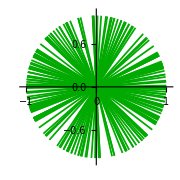
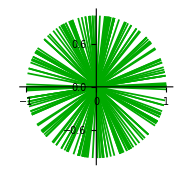
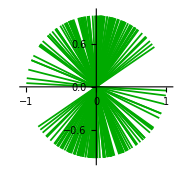
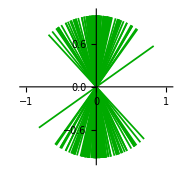
w1={-Graphics-,-Graphics-,-Graphics-,-Graphics-}

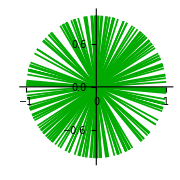
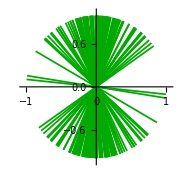
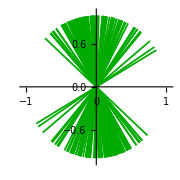
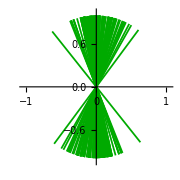
w0={-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Print["w1=",{fiberDist[w1Fang],fiberDist[w1FEang],fiberDist[w1E1ang],fiberDist[w1E2ang]}]
Print["w0=",{fiberDist[w0Fang],fiberDist[w0FEang],fiberDist[w0E1ang],fiberDist[w0E2ang]}]
```